IBM simulation of stochastic logistic model

birth prob per capita = α (1- N/k) 
death prob per capita = β

transform parameters by time

```mathematica
αstep:=α*δ;
βstep:=β*δ;
δ=0.1;
```

```mathematica
indsim[ninit_,tmax_]:=(nnow=ninit;
Table[newbirths = Sum[ RandomVariate[BinomialDistribution[1,(αstep*(1-nnow/k))]] ,{nnow}];
newdeaths= Sum[RandomVariate[BinomialDistribution[1,βstep]],{nnow}];
nnow=nnow+newbirths-newdeaths;
{t,nnow},{t,1,tmax}])
```

```mathematica
binsim[ninit_,tmax_]:=(nnow=ninit;
Table[newbirths = RandomVariate[BinomialDistribution[nnow,(αstep*(1-nnow/k))]];
newdeaths= RandomVariate[BinomialDistribution[nnow,βstep]];
nnow=nnow+newbirths-newdeaths;
{t,nnow},{t,1,tmax}])
```

```mathematica
k=40;α=0.2;β=0.1;
Timing[data=binsim[5,10000];]
```

{0.674429,Null}

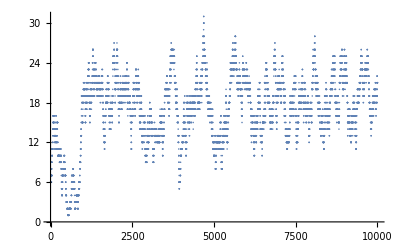

```mathematica
ListPlot[data]
```

```mathematica
Mean[Transpose[data][[2]]]//N
```

18.8529

```mathematica
k=40;α=0.2;β=0.1;
Timing[data=indsim[5,10000];]
```

{10.8085,Null}

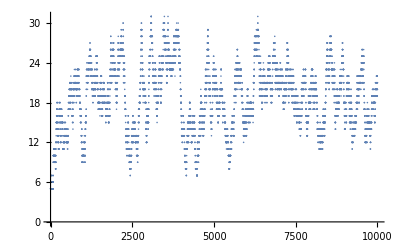

```mathematica
ListPlot[data]
```

```mathematica
Mean[Transpose[data][[2]]]//N
```

18.6672